```mathematica
KneserGraph[n_,r_]:=KneserGraph[n,r]=Graph[TwoWayRule@@@Select[Subsets[Subsets[Range[n],{r}],{2}],DisjointQ@@#&]]
```

```mathematica
DistanceKneserGraph[n_,r_]:=Sort[Subgraph[KneserGraph[n,r],#]&/@GroupBy[Subsets[Range[n],{r}],GraphDistance[KneserGraph[n,r],Range[r],#]&]]
```


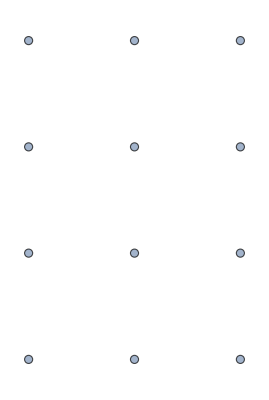
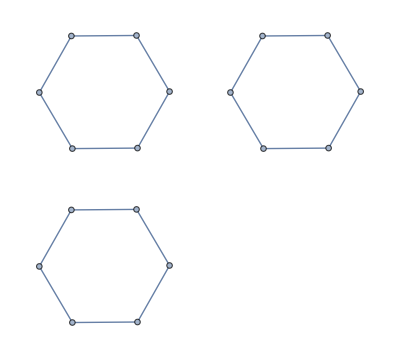
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-|>

```mathematica
DistanceKneserGraph[7,3]
```

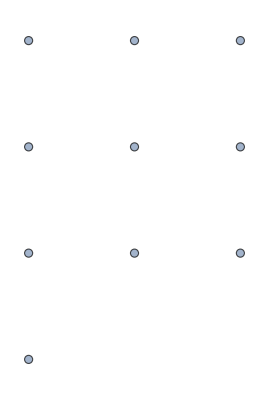
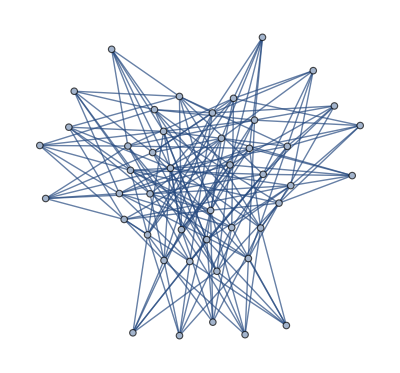
<|0→-Graphics-,1→-Graphics-,2→-Graphics-|>

```mathematica
DistanceKneserGraph[8,3]
```

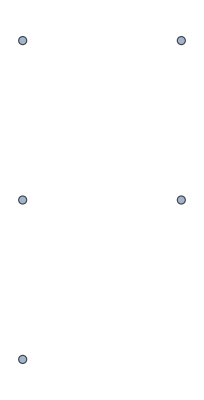
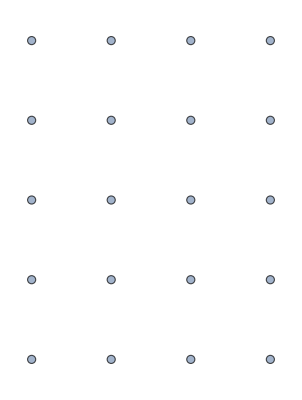
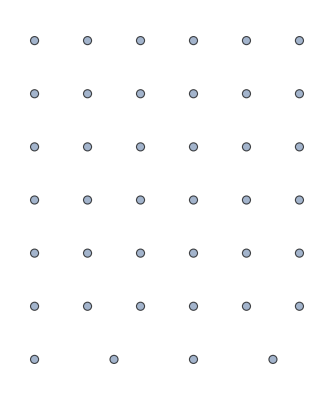
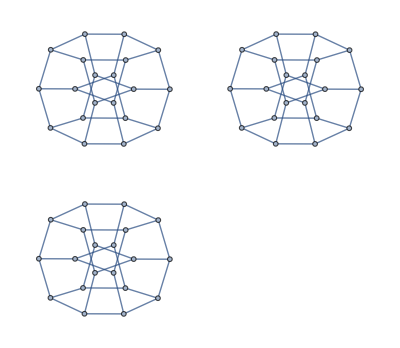
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>

```mathematica
DistanceKneserGraph[9,4]
```

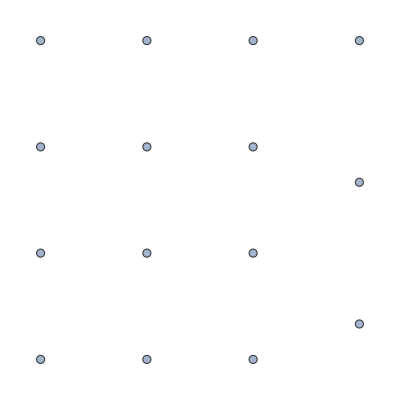
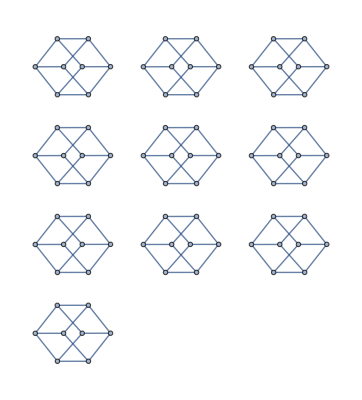
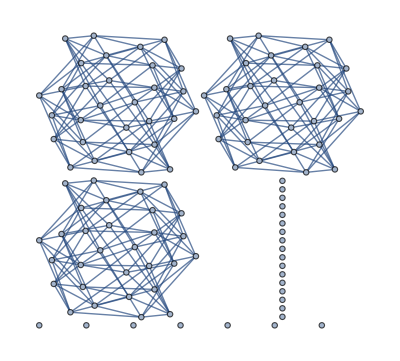
<|0→-Graphics-,1→-Graphics-,3→-Graphics-,2→-Graphics-|>

```mathematica
DistanceKneserGraph[10,4]
```

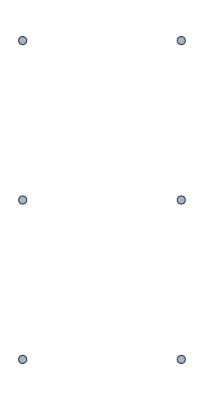
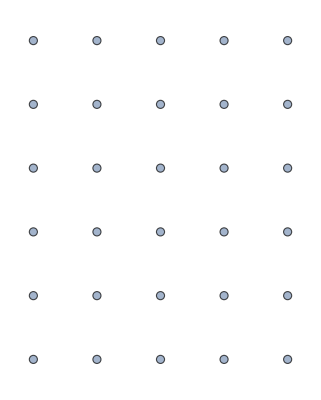
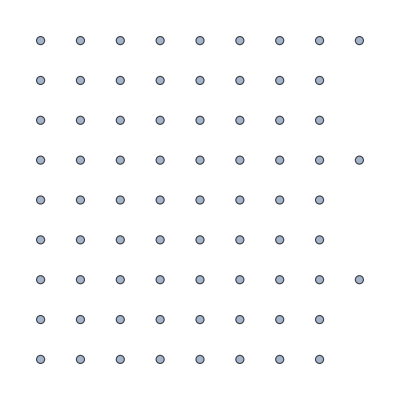
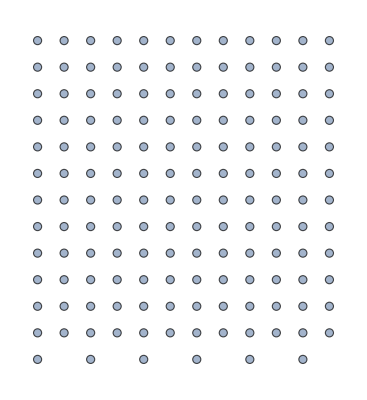
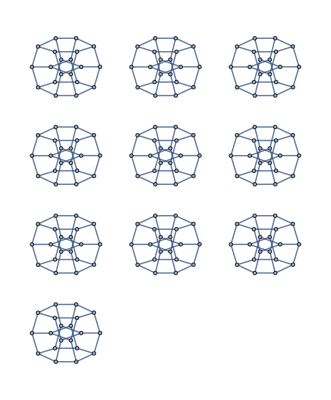
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-|>

```mathematica
DistanceKneserGraph[11,5]
```

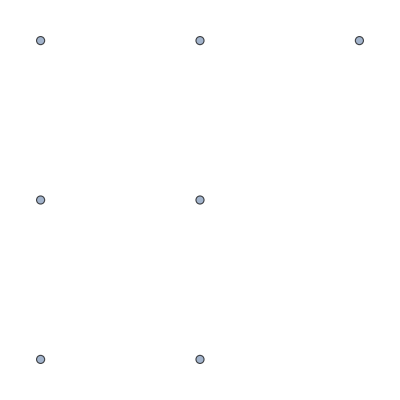
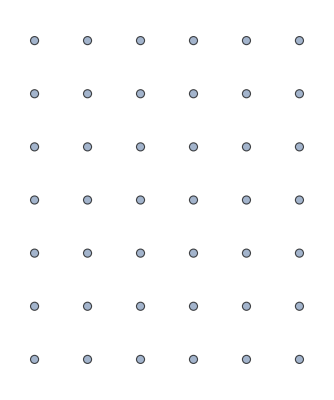
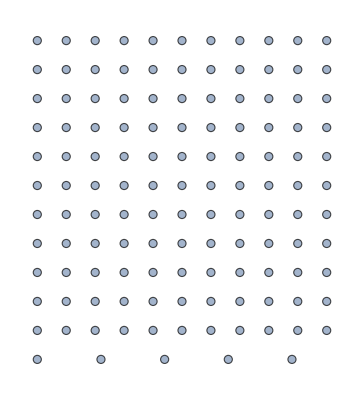
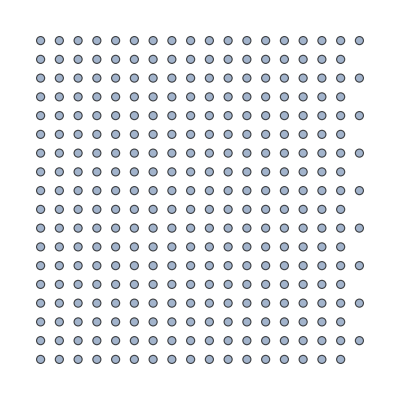
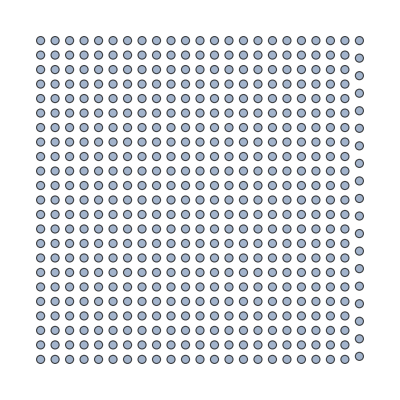
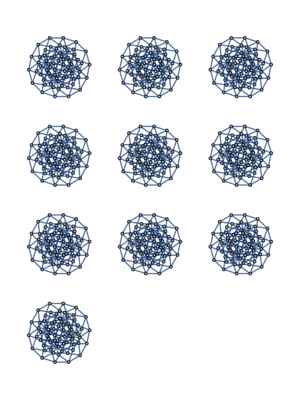
<|0→-Graphics-,1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,6→-Graphics-|>

```mathematica
DistanceKneserGraph[13,6]
```

```mathematica
ConnectedComponents[-Graphics-]
```

{{{1,4,5,6},{2,3,7,8},{2,3,7,9},{2,3,8,9},{1,4,5,9},{1,4,6,9},{1,4,5,8},{1,4,6,8},{1,4,5,7},{1,4,6,7},{2,3,6,7},{2,3,6,8},{2,3,5,7},{2,3,5,8},{2,3,6,9},{2,3,5,9},{1,4,8,9},{1,4,7,9},{1,4,7,8},{2,3,5,6}},{{1,3,5,6},{2,4,7,8},{2,4,7,9},{2,4,8,9},{1,3,5,9},{1,3,6,9},{1,3,5,8},{1,3,6,8},{1,3,5,7},{1,3,6,7},{2,4,6,7},{2,4,6,8},{2,4,5,7},{2,4,5,8},{2,4,6,9},{2,4,5,9},{1,3,8,9},{1,3,7,9},{1,3,7,8},{2,4,5,6}},{{1,2,5,6},{3,4,7,8},{3,4,7,9},{3,4,8,9},{1,2,5,9},{1,2,6,9},{1,2,5,8},{1,2,6,8},{1,2,5,7},{1,2,6,7},{3,4,6,7},{3,4,6,8},{3,4,5,7},{3,4,5,8},{3,4,6,9},{3,4,5,9},{1,2,8,9},{1,2,7,9},{1,2,7,8},{3,4,5,6}}}

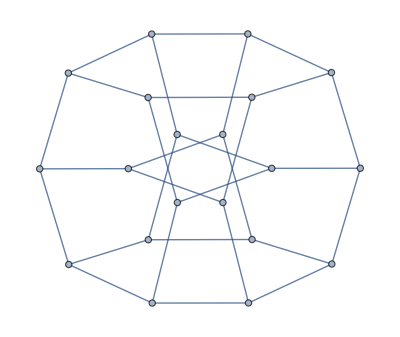

```mathematica
Subgraph[KneserGraph[9,4],First[%]]
```

```mathematica
IsomorphicGraphQ[%6,PetersenGraph[10,3]]
```

True